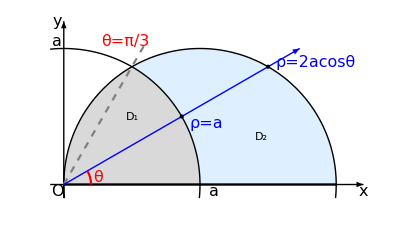

```mathematica
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(********绘图区+坐标系*******)
f1={
Graphics[{{White,Rectangle[{-0.2,-0.2},{2.2,1.2}]},
{Black,Arrowheads[0.03],Arrow[{{-0.1,0},{2.2,0}}]},
{Black,Arrowheads[0.03],Arrow[{{0,-0.1},{0,1.2}}]},
{Text[Style["x",tF,Italic],{2.2,-0.05}]},
{Text[Style["y",tF,Italic],{-0.05,1.2}]},
{Text[Style["O",tF,Italic],{-0.05,-0.05}]}
}]
};
(********平面区域*******)
f2={
RegionPlot[(x^2+y^2)<1&&x^2-2x+y^2<0,{x,0,1},{y,0,1},
PlotStyle->LightGray,BoundaryStyle->None],
RegionPlot[(x^2+y^2)>1&&x^2-2x+y^2<0,{x,0,2},{y,0,1},
PlotStyle->LightBlue,BoundaryStyle->None]
};
(********平面曲线*******)
f3={
ContourPlot[(x^2+y^2)==1,{x,-0.1,1},{y,-0.1,1},
ContourStyle->{Black,Thick}],
ContourPlot[x^2-2x+y^2==0,{x,0,2},{y,-0.1,1},
ContourStyle->{Black,Thick}]
};
(********点+辅助线*******)
f4={
Plot[Sqrt[3]x,{x,0,0.6},PlotStyle->{Gray,Dashed}],
Plot[0,{x,0,2},PlotStyle->{Black}],
Graphics[
{
{Blue,Arrowheads[0.03],Arrow[{{0,0},{2*Cos[Pi/6],2*Sin[Pi/6]}}]},
{PointSize[Large],Point[{Sqrt[3]Cos[Pi/6],Sqrt[3]Sin[Pi/6]}]},
{PointSize[Large],Point[{Cos[Pi/6],Sin[Pi/6]}]}
}
],
ParametricPlot[{0.2*Cos[t],0.2*Sin[t]},{t,0,Pi/6},
PlotStyle->{Red}
]
};
(********文字标记*******)
f5={
Graphics[{
{Text[Style["ρ=a",tF,Blue,Italic],{1.05,0.45}]},
{Text[Style["a",tF,Italic],{1.1,-0.05}]},
{Text[Style["a",tF,Italic],{-0.05,1.05}]},
{Text[Style["ρ=2acosθ",tF,Blue,Italic],{1.85,0.9}]},
{Text[Style["θ",tF,Red,Italic],{0.25,0.05}]},
{Text[Style["θ=π/3",tF,Red,Italic],{0.45,1.05}]},
{Text[Style["D_1",Large,Italic],{0.5,0.5}]},
{Text[Style["D_2",Large,Italic],{1.45,0.35}]}
}]
};
Show[f1,f2,f3,f4,f5]
```

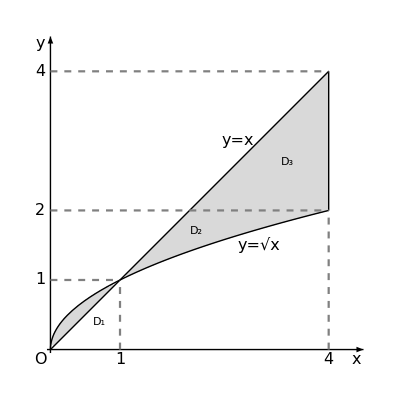

```mathematica
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(********绘图区+坐标系*******)
f1={
Graphics[{{White,Rectangle[{-0.2,-0.2},{4.5,4.5}]},
{Black,Arrowheads[0.03],Arrow[{{-0.05,0},{4.5,0}}]},
{Black,Arrowheads[0.03],Arrow[{{0,-0.05},{0,4.5}}]},
{Text[Style["x",tF,Italic],{4.4,-0.15}]},
{Text[Style["y",tF,Italic],{-0.15,4.4}]},
{Text[Style["O",tF,Italic],{-0.15,-0.15}]}
}]
};
(********平面区域*******)
f2={
RegionPlot[x<y<Sqrt[x]||Sqrt[x]<y<x,{x,0,4},{y,0,4},
PlotStyle->LightGray,BoundaryStyle->None,PlotPoints->40]
};
(********平面曲线*******)
f3={
Plot[x,{x,0,4},PlotStyle->{Black,Thick}],
Plot[Sqrt[x],{x,0,4},PlotStyle->{Black,Thick}],
ContourPlot[x==4,{x,2,4.2},{y,2,4},ContourStyle->{Black,Thick}]
};
(********点+辅助线*******)
f4={
Plot[2,{x,0,4},PlotStyle->{Gray,Dashed}],
Plot[1,{x,0,1},PlotStyle->{Gray,Dashed}],
Plot[4,{x,0,4},PlotStyle->{Gray,Dashed}],
ContourPlot[x==1,{x,0,2},{y,0,1},ContourStyle->{Gray,Dashed}],
ContourPlot[x==4,{x,2,4.2},{y,0,2},ContourStyle->{Gray,Dashed}]
};
(********文字标记*******)
f5={
Graphics[{
{Text[Style["1",tF],{1,-0.15}]},
{Text[Style["4",tF],{4,-0.15}]},
{Text[Style["1",tF],{-0.15,1}]},
{Text[Style["2",tF],{-0.15,2}]},
{Text[Style["4",tF],{-0.15,4}]},
{Text[Style["y=x",tF,Italic],{2.7,3.0}]},
{Text[Style["y=√x",tF,Italic],{3,1.5}]},
{Text[Style["D_1",Large,Italic],{0.7,0.4}]},
{Text[Style["D_2",Large,Italic],{2.1,1.7}]},
{Text[Style["D_3",Large,Italic],{3.4,2.7}]}
}]
};
Show[f1,f2,f3,f4,f5]
```

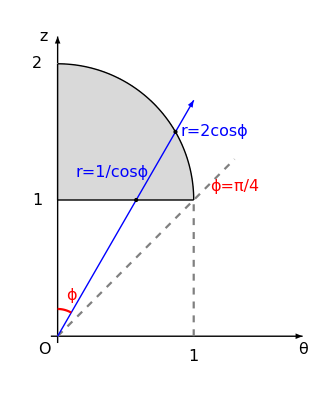

```mathematica
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(********绘图区+坐标系*******)
f1={
Graphics[{{White,Rectangle[{-0.2,-0.2},{1.8,2.2}]},
{Black,Arrowheads[0.03],Arrow[{{-0.05,0},{1.8,0}}]},
{Black,Arrowheads[0.03],Arrow[{{0,-0.05},{0,2.2}}]},
{Text[Style["θ",tF],{1.8,-0.1}]},
{Text[Style["z",tF,Italic],{-0.1,2.2}]},
{Text[Style["O",tF,Italic],{-0.1,-0.1}]}
}]
};
(********平面区域*******)
f2={
RegionPlot[x^2+(y-1)^2<1,{x,0,1},{y,1,2},
PlotStyle->LightGray,BoundaryStyle->None,PlotPoints->40]
};
(********平面曲线*******)
f3={
Plot[1,{x,0,1},PlotStyle->{Black,Thick}],
ContourPlot[x==0,{x,-0.1,1},{y,1,2},ContourStyle->{Black,Thick}],
ContourPlot[x^2+(y-1)^2==1,{x,0,1},{y,1,2},ContourStyle->{Black,Thick}]
};
(********点+辅助线*******)
f4={
Plot[x,{x,0,1.3},PlotStyle->{Gray,Dashed}],
ContourPlot[x==1,{x,0,2},{y,0,1},ContourStyle->{Gray,Dashed}],
Graphics[
{
{Blue,Arrowheads[0.03],Arrow[{{0,0},{2*Cos[Pi/3],2*Sin[Pi/3]}}]},
{PointSize[Large],Point[{1/Sqrt[3],1}]},
{PointSize[Large],Point[{Sqrt[3]Cos[Pi/3],Sqrt[3]Sin[Pi/3]}]}
}
],
ParametricPlot[{0.2*Cos[t],0.2*Sin[t]},{t,Pi/3,Pi/2},
PlotStyle->{Red}]
};
(********文字标记*******)
f5={
Graphics[{
{Text[Style["1",tF],{1,-0.15}]},
{Text[Style["1",tF],{-0.15,1}]},
{Text[Style["2",tF],{-0.15,2}]},
{Text[Style["ϕ=π/4",tF,Red],{1.3,1.1}]},
{Text[Style["ϕ",tF,Red],{0.1,0.3}]},
{Text[Style["r=2cosϕ",tF,Blue,Italic],{1.15,1.5}]},
{Text[Style["r=1/cosϕ",tF,Blue,Italic],{0.4,1.2}]}
}]
};
Show[f1,f2,f3,f4,f5]
```